```mathematica
Residue[x^(ν+1)/x^(2 ν+1)/.ν-> 1/2,{x,0}]
```

Residue[1/(√x),{x,0}]

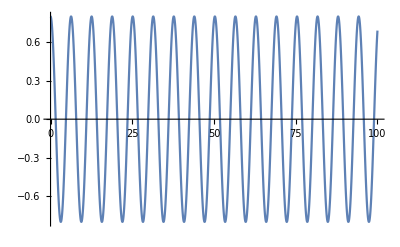

```mathematica
Plot[x^(1/2)BesselJ[-1/2, x], {x, 0, 100}]
```

```mathematica
BesselJ[-1/2,0]
```

ComplexInfinity

```mathematica
Gamma[0-1/2+1]
```

√π

```mathematica
x DiracDelta[x]/.DiracDelta[x]-> DiracDelta[1/x]
```

x DiracDelta[1/x]

```mathematica
Integrate[DiracDelta[y]DiracDelta[x-y], {x,-2 y, 2 y}, Assumptions->{y>0}]
```

0

```mathematica
(Integrate[Exp[-x^2/(4 σ^2)], {x, -Infinity,Infinity}, Assumptions->{σ>0}]Exp[π^4/(16 h^2 σ^2)-π^2/(2 h)])/(Integrate[x^(1/2)BesselJ[-1/2,x]Exp[-x^2/(4 σ^2)], {x, 0, Infinity}, Assumptions->{σ>0}])
```

ⅇ^(-π^2/(2 h)+π^4/(16 h^2 σ^2)+σ^2) √(2 π)

```mathematica
Solve[D[%347,h] == 0,h]
```

{{h→π^2/(4 σ^2)}}

```mathematica
%347/.h-> π^2/(4 σ^2)
```

√(2 π)

```mathematica
Plot3D[Exp[π^4/(16 h^2 σ^2)-π^2/(2 h)], {h, 0.001,1}, {σ, 0.001, 10}]
```

-Graphics3D-

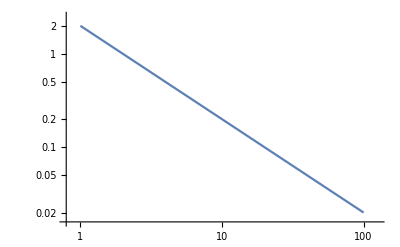

```mathematica
LogLogPlot[((2^(3/2)(Exp[π^4/(16 h^2 σ^2)-π^2/(2 h)]))/(Sqrt[2]Exp[-σ^2]σ))/.h-> π^2/(4 σ^2), {σ, 1,100}]
```

```mathematica
LogLogPlot[2/σ, {σ,1,100}]
```

-Graphics-

```mathematica
n = (400 σ^2)/π^2/.σ-> 1 //N
```

40.5285

```mathematica
Solve[R ==  π^2/(4 σ^2) n,n]
```

{{n→(4 R σ^2)/π^2}}

```mathematica
Integrate[x^(1/2)BesselJ[-1/2,x]Exp[-x^2/(4 σ^2)], {x, 0, Infinity}, Assumptions->{σ>0}]
```

√2 ⅇ^(-σ^2) σ

```mathematica
Solve[D[2^(3/2)(Exp[π^4/(16 h^2 σ^2)-π^2/(2 h)]), h] == 0, h]
```

{{h→π^2/(4 σ^2)}}

```mathematica
h/.Solve[R == π n Tanh[π/2 Sinh[h n]], h]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{0.024674 ArcSinh[0.63662 ArcTanh[0.00785398 R]]}

```mathematica
Solve[ArcSinh[(2 ArcTanh[R/(n π)])/π]/n == π^2/(4 σ^2), n]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[ArcSinh[(2 ArcTanh[R/(n π)])/π]/n==π^2/(4 σ^2),n]

General::ovfl: Overflow occurred in computation.

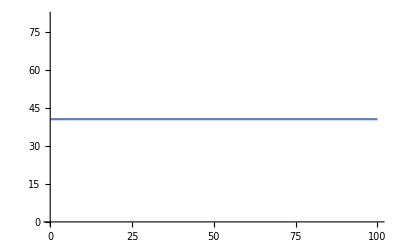

```mathematica
Plot[n/.NSolve[10 == π n Tanh[π/2 Sinh[π^2/(4 σ^2)n]],n], {σ,0.1,100}]
```

```mathematica
n/.NSolve[10 == π n Tanh[π/2 Sinh[π^2/(4 1^2)n]],n]
```

40.5285

```mathematica
Integrate[x^(1/2)BesselJ[-1/2,x]Exp[-x^2/(4 σ^2)], {x,R, Infinity}, Assumptions->{R>0,σ>0}]
```

(ⅇ^(-σ^2) σ (Erfc[R/(2 σ)-ⅈ σ]+Erfc[R/(2 σ)+ⅈ σ]))/(√2)

```mathematica
Simplify[ComplexExpand[1/4 (Erfc[R/(2 σ)-ⅈ σ]+Erfc[R/(2 σ)+ⅈ σ])], Assumptions->{R>2 σ>0}]
```

1/4 (ⅈ Im[Erfc[R/(2 σ)-ⅈ σ]]+ⅈ Im[Erfc[R/(2 σ)+ⅈ σ]]+Re[Erfc[R/(2 σ)-ⅈ σ]]+Re[Erfc[R/(2 σ)+ⅈ σ]])

```mathematica
1/4 (Erfc[R/(2 σ)-ⅈ σ]+Erfc[R/(2 σ)+ⅈ σ])/.R-> 10 π
```

1/4 (Erfc[(5 π)/σ-ⅈ σ]+Erfc[(5 π)/σ+ⅈ σ])

```mathematica
Clear[n]
Plot3D[Log10[Abs[1/4 (Erfc[(π^2 n)/(8 σ^3)-ⅈ σ]+Erfc[(π^2 n)/(8 σ^3)+ⅈ σ])]],{σ, 0.1, 3},{n,1,50},PlotRange->{Full,Full,{-1,0}}]
```

-Graphics3D-

```mathematica
Exp[-2]//N
```

0.135335

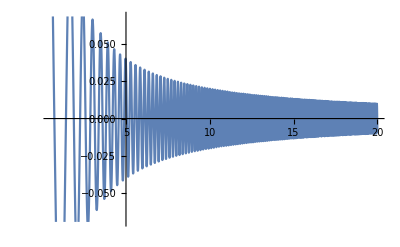

```mathematica
Plot[1/4 (Erfc[σ-ⅈ σ]+Erfc[σ+ⅈ σ]),{σ,0.5,20}]
```

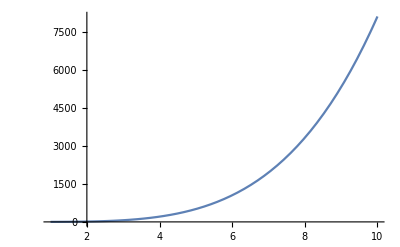

```mathematica
Plot[8/π^2 σ^4,{σ,1,10}]
```

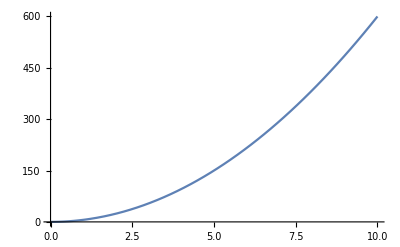

```mathematica
Plot[6 σ^2,{σ,0,10}]
```

```mathematica
Reduce[D[1/4 (Erfc[(π^2 n)/(8 σ^3)-ⅈ σ]+Erfc[(π^2 n)/(8 σ^3)+ⅈ σ]),σ] == 0,n]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[1/4 (-(2 ⅇ^(-((n π^2)/(8 σ^3)-ⅈ σ)^2) (-ⅈ-(3 n π^2)/(8 σ^4)))/(√π)-(2 ⅇ^(-((n π^2)/(8 σ^3)+ⅈ σ)^2) (ⅈ-(3 n π^2)/(8 σ^4)))/(√π))==0,n]

```mathematica
Simplify[D[1/4 (ⅈ Im[Erfc[R/(2 σ)-ⅈ σ]]+ⅈ Im[Erfc[R/(2 σ)+ⅈ σ]]+Re[Erfc[R/(2 σ)-ⅈ σ]]+Re[Erfc[R/(2 σ)+ⅈ σ]]),R], Assumptions->{R>0,σ>0}]
```

-1/(4 √π σ)ⅈ ⅇ^(-((R+2 ⅈ σ^2)^2)/(4 σ^2)) (ⅇ^(2 ⅈ R) Im'[Erfc[R/(2 σ)-ⅈ σ]]+Im'[Erfc[R/(2 σ)+ⅈ σ]]-ⅈ (ⅇ^(2 ⅈ R) Re'[Erfc[R/(2 σ)-ⅈ σ]]+Re'[Erfc[R/(2 σ)+ⅈ σ]]))

```mathematica
Simplify[ComplexExpand[1/4 (Erfc[R/(2 σ)-ⅈ σ]+Erfc[R/(2 σ)+ⅈ σ])],Assumptions->{σ>0,R>0}]
```

1/4 (ⅈ Im[Erfc[R/(2 σ)-ⅈ σ]]+ⅈ Im[Erfc[R/(2 σ)+ⅈ σ]]+Re[Erfc[R/(2 σ)-ⅈ σ]]+Re[Erfc[R/(2 σ)+ⅈ σ]])

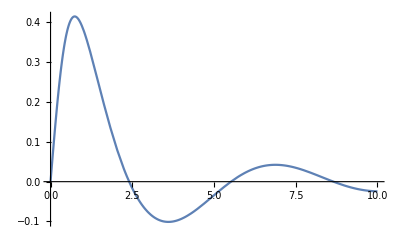

```mathematica
Plot[(x BesselJ[0,x])/(x^2+1),{x,0,10}]
```

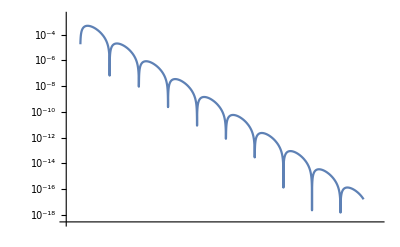

```mathematica
LogLogPlot[Abs[(1/4 (Erfc[π^2/(8 σ^3)n-ⅈ σ]+Erfc[π^2/(8 σ^3)n+ⅈ σ]))/.σ-> 20],{n,130000,135000}]
```

```mathematica
LogLogPlot[2/σ Exp[π^4/(16 h^2 σ^2)-π^2/(2 h)+σ^2]+Abs[((ⅇ^(-σ^2) σ (Erfc[R/(2 σ)-ⅈ σ]+Erfc[R/(2 σ)+ⅈ σ]))/(√2))/.n-> 30/.σ-> 5],{h,0.1,2}, PlotRange->{Full,{10^0,10^8}}]
```

```mathematica
0
```

```mathematica
10^0.2
```

1.58489

```mathematica
Integrate[Exp[-u^2/(4 σ^2)+I u], {u,-Infinity,Infinity}, Assumptions->{σ>0}]
```

2 ⅇ^(-σ^2) √π σ

```mathematica
Integrate[Exp[-u^2/(4 σ^2)+I u], {x,-Infinity,Rp}, Assumptions->{σ>0,Rp>0}]+Integrate[Exp[-u^2/(4 σ^2)-I u], {u,-Infinity,Rp}, Assumptions->{σ>0,Rp>0}]
```

ⅇ^(-σ^2) √π σ (1+Erf[Rp/(2 σ)-ⅈ σ])

```mathematica
(Integrate[Exp[-(x+I y)^2/(4 σ^2)+I (x+I y)], {x,-Infinity,Rp}, Assumptions->{σ>0,Rp>0,y>0}]+Integrate[Exp[-(x-I y)^2/(4 σ^2)+I (x-I y)], {x,Rp,-Infinity}, Assumptions->{σ>0,Rp>0,y>0}])/.y-> π^2/(2 h)/.Rp-> h n/.σ-> 5
```

(5 √π (1+Erf[1/10 (h n+ⅈ (-50+π^2/(2 h)))]))/ⅇ^25+(5 ⅈ √π (ⅈ+Erfi[1/10 (50+ⅈ h n+π^2/(2 h))]))/ⅇ^25

```mathematica
Plot3D[Abs[%377], {h,0.1,1},{n,1,20}]
```

-Graphics3D-

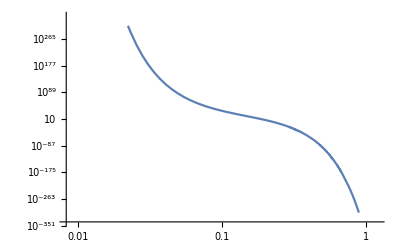

```mathematica
LogLogPlot[{Abs[((5 √π (1+Erf[1/10 (h n+ⅈ (-50+π^2/(2 h)))]))/ⅇ^25+(5 ⅈ √π (ⅈ+Erfi[1/10 (50+ⅈ h n+π^2/(2 h))]))/ⅇ^25)/.n-> 300]},{h,0.01,1}]
```

```mathematica
Integrate[x^(1/2)BesselJ[-1/2,x]Exp[-x^2/(4 σ^2)], {x,R, Infinity}, Assumptions->{R>0,σ>0}]/.σ-> 5/.R-> h n
```

(5 (Erfc[-5 ⅈ+(h n)/10]+Erfc[5 ⅈ+(h n)/10]))/(√2 ⅇ^25)

```mathematica
Exp[-(λ I+1)y]Integrate[Exp[Sqrt[λ^2+1] x],{x,-Infinity,Rp}, Assumptions->{λ>0,y>0,Rp>0}]
```

(ⅇ^(y (-1-ⅈ λ)+Rp √(1+λ^2)))/(√(1+λ^2))

```mathematica
Simplify[Limit[Integrate[Exp[(- λ+I) x],x],x-> Infinity], Assumptions->{λ>0}]
```

Limit[-ⅇ^(-x (-ⅈ+λ))/(-ⅈ+λ),x→∞]

```mathematica
Integrate[Exp[-λ(x+I y)+I(x+I y)],{x,-Rp,Rp}, Assumptions->{λ>0,Rp>0,y>0}]+Integrate[Exp[-λ(x-I y)+I(x-I y)],{x,Rp,-Rp}, Assumptions->{λ>0,Rp>0,y>0}]
```

(ⅇ^((Rp+ⅈ y) (-ⅈ+λ)) (-1+ⅇ^(-2 Rp (-ⅈ+λ))))/(-ⅈ+λ)+(ⅇ^(-(Rp+ⅈ y) (-ⅈ+λ)) (-1+ⅇ^(2 Rp (-ⅈ+λ))))/(-ⅈ+λ)

```mathematica
Simplify[Abs[ComplexExpand[%422]], Assumptions->{y>0,λ>0,Rp>0}]
```

ⅇ^(-y-Rp λ) Abs[1/(-ⅈ+λ)((-1+ⅇ^(2 Rp λ)) Cos[Rp]-ⅈ (1+ⅇ^(2 Rp λ)) Sin[Rp]) ((-1+ⅇ^(2 y)) Cos[y λ]+ⅈ (1+ⅇ^(2 y)) Sin[y λ])]

```mathematica
Plot[%425/.y-> π^2/(2 h)/.λ-> 10/.Rp-> h n/. n-> 500,{h,0.024,0.025}]
```

-Graphics-

```mathematica
(x-I y)^4//Expand
```

x^4-4 ⅈ x^3 y-6 x^2 y^2+4 ⅈ x y^3+y^4

```mathematica
D[(x^4-4 ⅈ x^3 y-6 x^2 y^2+4 ⅈ x y^3+y^4), x]
```

4 x^3-12 ⅈ x^2 y-12 x y^2+4 ⅈ y^3

```mathematica
(x+I y)^2//Expand
```

x^2+2 ⅈ x y-y^2

```mathematica
Integrate[z Exp[-z^2+2 π I z/h],{z,-Infinity,Infinity}, Assumptions->{h>0}]
```

(ⅈ ⅇ^(-π^2/h^2) π^(3/2))/h

```mathematica
Residue[x/BesselJ[0, (π x)/h],{x,BesselJZero[0,1]}]
```

0

```mathematica
BesselJ[0, (π x)/h]
```

```mathematica
Integrate[Exp[(I π)/h z-π^2/(4 σ^2 h^2)z^2],{z,-Infinity,Infinity}, Assumptions->{h>0,σ>0}]
```

(2 ⅇ^(-σ^2) h σ)/(√π)

```mathematica
ψ[z_] = z Tanh[π/2 Sinh[z]]
```

z Tanh[1/2 π Sinh[z]]

```mathematica
ψ'[x+I y]
```

1/2 π (x+ⅈ y) Cosh[x+ⅈ y] Sech[1/2 π Sinh[x+ⅈ y]]^2+Tanh[1/2 π Sinh[x+ⅈ y]]

```mathematica
Plot3D[Abs[%482],{x,-10,10},{y,-10,10},PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[Abs[ψ[x+I y]],{x,-10,10},{y,-π/2,3 π/2}]
```

-Graphics3D-

```mathematica
Solve[D[I π/h z -1/(4 σ^2)(π/h z)^2+Log[ψ'[z]],z] == 0,z]
```

Solve[(ⅈ π)/h-(π^2 z)/(2 h^2 σ^2)+(π Cosh[z] Sech[1/2 π Sinh[z]]^2+1/2 π z Sech[1/2 π Sinh[z]]^2 Sinh[z]-1/2 π^2 z Cosh[z]^2 Sech[1/2 π Sinh[z]]^2 Tanh[1/2 π Sinh[z]])/(1/2 π z Cosh[z] Sech[1/2 π Sinh[z]]^2+Tanh[1/2 π Sinh[z]])==0,z]

```mathematica
ψ'[z]
```

1/2 π z Cosh[z] Sech[1/2 π Sinh[z]]^2+Tanh[1/2 π Sinh[z]]

```mathematica
Solve[(ⅈ π)/h-(π^2 z)/(2 h^2 σ^2)+(π Cosh[z] Sech[1/2 π Sinh[z]]^2+1/2 π z Sech[1/2 π Sinh[z]]^2 Sinh[z]-1/2 π^2 z Cosh[z]^2 Sech[1/2 π Sinh[z]]^2 )/(1/2 π z Cosh[z] Sech[1/2 π Sinh[z]]^2)==0,z]
```

```mathematica
Integrate[Exp[- π^2/h^2 u^2/(4 σ^2)+I u π/h], {u,-Infinity,Infinity}, Assumptions->{h>0,σ>0}]
```

(2 ⅇ^(-σ^2) h σ)/(√π)

```mathematica
Simplify[(Integrate[Exp[-u^2/(4 σ^2)+ I u],{u,Rp,Infinity}, Assumptions->{σ>0,Rp>0}]-Integrate[Exp[-u^2/(4 σ^2)+ I u],{u,-Infinity,-Rp}, Assumptions->{σ>0,Rp>0}])/(Integrate[x^(1/2)BesselJ[-1/2,x]Exp[-x^2/(4 σ^2)],{x,0,Infinity}, Assumptions->{σ>0}]),Assumptions->{σ>0}]
```

√(π/2) (Erfc[Rp/(2 σ)-ⅈ σ]-Erfc[Rp/(2 σ)+ⅈ σ])

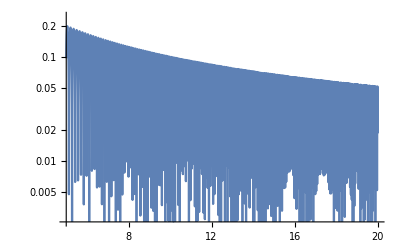

```mathematica
LogPlot[Abs[(√(π/2) (Erfc[Rp/(2 σ)-ⅈ σ]-Erfc[Rp/(2 σ)+ⅈ σ]))/.Rp-> 1.9999 σ^2],{σ, 5,20}]
```

```mathematica
Integrate[x^(1/2)BesselJ[-1/2,x]Exp[-x^2/(4 σ^2)],{x,0,Infinity}, Assumptions->{σ>0}]
```

√2 ⅇ^(-σ^2) σ

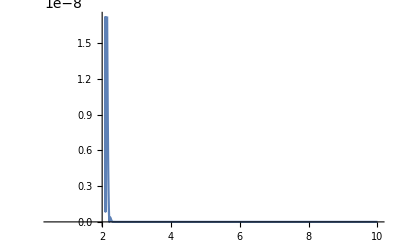

```mathematica
Plot[Abs[%518/.Rp-> 2 σ^3], {σ,0.5,10}]
```

```mathematica
Plot3D[Log10[Abs[(%518/.Rp-> h n+1/2 (Erfc[(h n)/(2 σ)-ⅈ σ]+Erfc[(h n)/(2 σ)+ⅈ σ]))/.σ -> 10]], {h,0.01,1}, {n, 30, 400}]
```

-Graphics3D-

```mathematica
Integrate[x^(1/2)BesselJ[-1/2,x]Exp[-x^2/(4 σ^2)], {x, h n, Infinity}, Assumptions->{h>0,n>0,σ>0}]/(Integrate[x^(1/2)BesselJ[-1/2,x]Exp[-x^2/(4 σ^2)],{x,0,Infinity}, Assumptions->{σ>0}])
```

1/2 (Erfc[(h n)/(2 σ)-ⅈ σ]+Erfc[(h n)/(2 σ)+ⅈ σ])

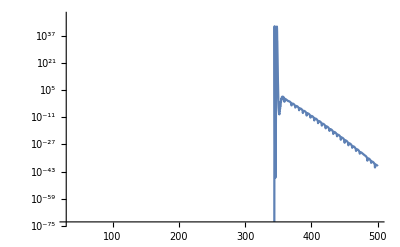

```mathematica
LogPlot[Abs[(%518/.Rp-> h n+1/2 (Erfc[(h n)/(2 σ)-ⅈ σ]+Erfc[(h n)/(2 σ)+ⅈ σ]))/.σ -> 10/.h-> 0.55], {n, 30, 500}]
```

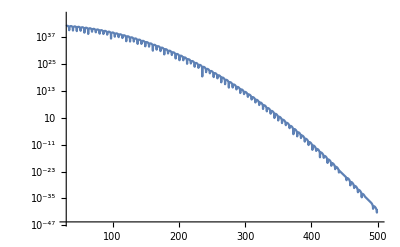

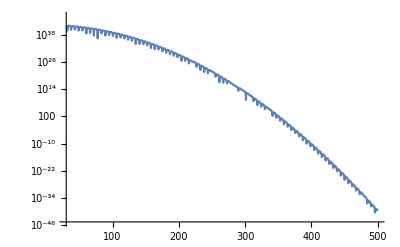

```mathematica
LogPlot[Abs[(1/2 (Erfc[(h n)/(2 σ)-ⅈ σ]+Erfc[(h n)/(2 σ)+ⅈ σ]))/.σ -> 10/.h-> 0.55], {n, 30, 500}]
LogPlot[Abs[((√(π/2) (Erfc[Rp/(2 σ)-ⅈ σ]-Erfc[Rp/(2 σ)+ⅈ σ]))/.Rp-> h n)/.σ -> 10/.h-> 0.55], {n, 30, 500}]
```

```mathematica
Integrate[Exp[-x^2/(4 σ^2)],{x,Rp,Infinity}, Assumptions->{σ>0,Rp>0}]-Integrate[Exp[-x^2/(4 σ^2)],{x,-Infinity,-Rp}, Assumptions->{σ>0,Rp>0}]
```

0

```mathematica
Integrate[x^(1/2)BesselJ[-1/2,x]Exp[-x^2/(4 σ^2)],{x,R,Infinity}, Assumptions->{R>0,σ>0}]/(Integrate[x^(1/2)BesselJ[-1/2,x]Exp[-x^2/(4 σ^2)],{x,0,Infinity}, Assumptions->{σ>0}])
```

1/2 (Erfc[R/(2 σ)-ⅈ σ]+Erfc[R/(2 σ)+ⅈ σ])

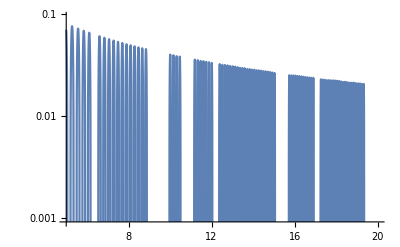

```mathematica
LogPlot[%589/.R->  2 σ^2, {σ, 5,20}]
```

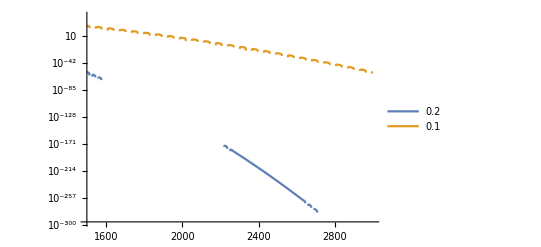

```mathematica
LogPlot[{%589/.R->  0.2*n/.σ-> 10,%589/.R->  0.1*n/.σ-> 10}, {n, 1500,3000},PlotLegends->{"0.2","0.1"}]
```

```mathematica
200^2/(4 * 10^2)
```

100

```mathematica
(Integrate[x^(1/2)BesselJ[-1/2,x]Exp[-x^2/(4 σ^2)],{x,0,Infinity}, Assumptions->{σ>0}])/.σ-> 10//N
```

5.26098×10^-43

```mathematica
Plot3D[Re[(x+I y)Tanh[π/2 Sinh[x+I y]]], {x,-10,10},{y,-π/2,π/2}]
```

-Graphics3D-

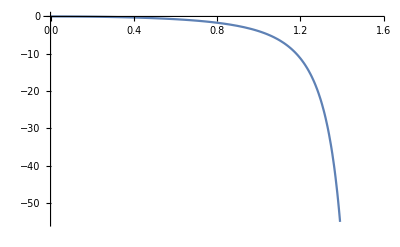

```mathematica
Plot[I y Tanh[π/2 Sinh[I y]], {y,0,π/2}]
```